# Subspace recompilation for BCS Hamiltonian

Set environment, such as threads, gpu, etc.

```mathematica
(*SetEnvironment["OMP_NUM_THREADS"->"8"]*)
(*SetDirectory[NotebookDirectory[]];*)
```

Load the QuESTLink

```mathematica
(*Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_gpu"];*)
```

### Modules

```mathematica
GetBlocks::usage="GetBlocks[blockdiagmat_,draw_:True]. Partition indices of a matrix by its blocks.";
GetBlocks[mat_,draw_:True]:=Module[{adjmat,dim=Length@mat,graph},
adjmat=ConstantArray[0,{dim,dim}];
Table[adjmat⟦i,j⟧=If[mat⟦i,j⟧==0,0,1],{i,dim},{j,dim}];
graph=AdjacencyGraph@adjmat;
If[draw,Print@graph];
ConnectedComponents@graph-1
]
```

## BCS simulation

```mathematica
(* non-iteracting harmonic oscillator-type energy levels *)
ϵ=ω(#+0.5)&/@Range[0,4];
(* time-dependent coupling function *)
coupling[t_,g0_,gc_]:=ExpandAll[
(ArcTan[(t-t1)J/(ℏ Γ)]+π/2)(ArcTan[(t2-t)J/(ℏ Γ)]+π/2)(gc-g0)/π^2+g0
]
```

```mathematica
constants={
(* time start to quench and reverse. J is an arbitrary energy unit *)
t1->9 ℏ/J,
t2->18 ℏ/J,
(* initial coupling constant*)
Γ->0.1,
(* frequency *)
ω->5J/3
};
```

```mathematica
(* mean-field eigenvalues *)
Ej[ϵ_,Δ_]:=Sqrt[ϵ^2+Abs[Δ]^2]
(* superconducting gap *)
(*2/g=∑_k 1/Subscript[E, k] tanh[Subscript[E, k]/(2 Subscript[k, b] Temp)]*)
(* since we consider temperature Temp=0, tanh(∞)=1 *)
(* Superconducting gaps*)
Δ0=J;
Δc=2J;
```

```mathematica
g0=2 /Total[1/Ej[ϵ,Δ0]];
gc=2/ Total[1/Ej[ϵ,Δc]];
```

The entire BCS Hamiltonian

```mathematica
Hgaudin[q_,n_,ϵ_,g_]:=Total@Table[({Subscript[X, q],Subscript[Y, q],Subscript[Z, q]}.{Subscript[X, j],Subscript[Y, j],Subscript[Z, j]})/(2(ϵ[[q+1]]-ϵ[[j+1]])), {j,Complement[Range[0,n-1],{q}]}]+Subscript[Z, q]/g
```

```mathematica
HBCS[n_,ϵ_,τ_]:=With[{g=coupling[τ*ℏ/Δ0,g0,gc]/.constants},
SimplifyPaulis@Chop@ExpandAll[
Total@Table[
Simplify[(-g ϵ[[q+1]]+g^2/2)Hgaudin[q,n,ϵ,g]/Δ0/.constants,J>0]
,{q,n-1}]+
SimplifyPaulis@Chop@ExpandAll[SimplifyPaulis@Simplify[g^3/(4Δ0)*(Total@Table[Hgaudin[q,n,ϵ,g],{q,0,n-1}])^2/.constants,J>0]]
]
]
```

Constants

```mathematica
(*mean field-eigenvalues*)
ej=Simplify[Ej[ϵ,Δ0]/.constants,J>0];
(* |Subscript[v, j]|^2, |Subscript[u, j]|^2 *)
ujs=Simplify[0.5(1+ϵ/ej)/.constants,J>0];
vjs=Simplify[0.5(1-ϵ/ej)/.constants,J>0];
```

```mathematica
(*  
Subscript[u, j] 0-Subscript[v, j] 1;
Ry[θ]0=Cos[θ/2]0-Sin[θ/2]1 
 *)
θinit=2*ArcCos@Sqrt@ujs;
```

initial states and memory allocation

```mathematica
DestroyAllQuregs[]
{ψexact,ψinitexact}=CreateQuregs[5,2];
```

```mathematica
(*exact groundstate*)
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=eigvec[[First@Ordering[eigval,1]]];
SetQuregMatrix[ψinitexact,initv];
```

## Obtain the expression ⅇ^(-i δt H_BCS)

```mathematica
(* Medium resolution *)
τs=Sort@DeleteDuplicates@Chop@Join[{0.,4.,8.},Range[8.,20.,0.2],{20.,23.5,27}]
(* the timesteps *)
δτ=Table[τs[[i]]-τs[[i-1]],{i,2,Length@τs}];
PrependTo[δτ,0];
(*sanity check*)
And@@Table[τs[[i]]==Total[δτ[[#]]&/@Range[i]],{i,Length@τs}]
(*τ=t J/ℏ*)
```

{0,4.,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.6,10.8,11.,11.2,11.4,11.6,11.8,12.,12.2,12.4,12.6,12.8,13.,13.2,13.4,13.6,13.8,14.,14.2,14.4,14.6,14.8,15.,15.2,15.4,15.6,15.8,16.,16.2,16.4,16.6,16.8,17.,17.2,17.4,17.6,17.8,18.,18.2,18.4,18.6,18.8,19.,19.2,19.4,19.6,19.8,20.,23.5,27}

True

The time-dependent gap Δ is controlled through g(t). Definition of g(t) is here

```mathematica
(*τ=t J/ℏ*)
```

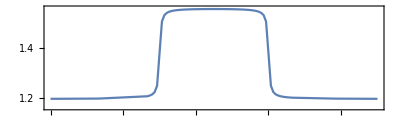

```mathematica
gvals=Simplify[(coupling[#*ℏ/Δ0,g0,gc]/Δ0&/@τs)//.constants,J>0];
ListPlot[Transpose@{τs,gvals},PlotRange->{1.16,1.56},Joined->True,AspectRatio->0.3,Frame->True,FrameTicks->{{Range[1,1.55,0.05],None},{Range[0,27,1],None}}]
```

```mathematica
rexactot2<<rexactot2.mx
```

{{0,1. Null},{4. Null,1. Null},{8. Null,1. Null},{8.2 Null,0.99998 Null},{8.4 Null,0.999947 Null},{8.6 Null,0.999914 Null},{8.8 Null,0.999863 Null},{9. Null,0.999582 Null},{9.2 Null,0.994672 Null},{9.4 Null,0.981143 Null},{9.6 Null,0.973563 Null},{9.8 Null,0.977681 Null},{10. Null,0.987941 Null},{10.2 Null,0.993529 Null},{10.4 Null,0.98836 Null},{10.6 Null,0.975568 Null},{10.8 Null,0.970874 Null},{11. Null,0.98325 Null},{11.2 Null,0.994077 Null},{11.4 Null,0.990444 Null},{11.6 Null,0.97977 Null},{11.8 Null,0.972743 Null},{12. Null,0.976647 Null},{12.2 Null,0.987961 Null},{12.4 Null,0.99523 Null},{12.6 Null,0.986169 Null},{12.8 Null,0.972178 Null},{13. Null,0.973483 Null},{13.2 Null,0.984802 Null},{13.4 Null,0.992672 Null},{13.6 Null,0.990067 Null},{13.8 Null,0.979478 Null},{14. Null,0.971512 Null},{14.2 Null,0.97669 Null},{14.4 Null,0.991584 Null},{14.6 Null,0.994419 Null},{14.8 Null,0.982465 Null},{15. Null,0.973332 Null},{15.2 Null,0.97477 Null},{15.4 Null,0.984827 Null},{15.6 Null,0.993177 Null},{15.8 Null,0.990692 Null},{16. Null,0.977343 Null},{16.2 Null,0.970184 Null},{16.4 Null,0.980813 Null},{16.6 Null,0.992501 Null},{16.8 Null,0.992048 Null},{17. Null,0.982935 Null},{17.2 Null,0.97415 Null},{17.4 Null,0.975249 Null},{17.6 Null,0.986292 Null},{17.8 Null,0.996358 Null},{18. Null,0.992191 Null},{18.2 Null,0.989091 Null},{18.4 Null,0.990879 Null},{18.6 Null,0.992256 Null},{18.8 Null,0.992756 Null},{19. Null,0.992674 Null},{19.2 Null,0.992299 Null},{19.4 Null,0.991953 Null},{19.6 Null,0.99189 Null},{19.8 Null,0.992207 Null},{20. Null,0.992498 Null},{23.5 Null,0.992259 Null},{27. Null,0.992215 Null}}

Rerun everything

```mathematica
bcscompilecssrerun={};
```

0.

**** Compile @Thu 29 Dec 2022 02:50:54 τ=0.; δ0 ****

Cycle 1@Thu 29 Dec 2022 02:56:37 adjust hyperparams, slowdown:True

τ=0.; δ=0; cost=2.22045×10^-16; ngates=0; runtime=5.71379 min

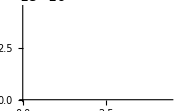

-Graphics-

**** Compile @Thu 29 Dec 2022 02:56:37 τ=0.; δ4. ****

τ=4.; δ=4.; cost=2.57775×10^-6; ngates=46; runtime=6.77882 min

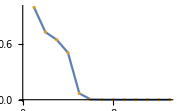

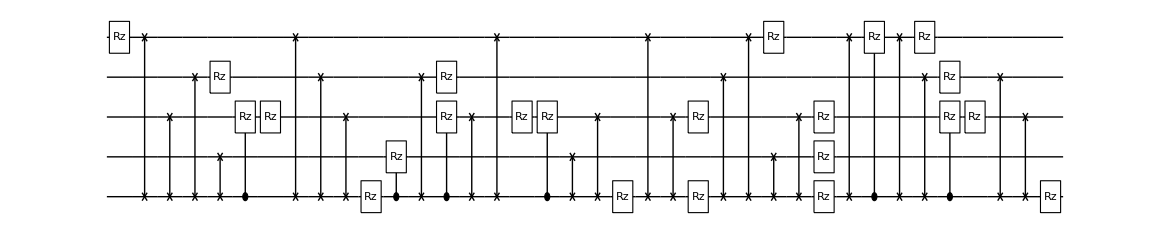

**** Compile @Thu 29 Dec 2022 03:03:24 τ=4.; δ4. ****

τ=8.; δ=4.; cost=3.71413×10^-6; ngates=47; runtime=8.47525 min

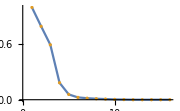

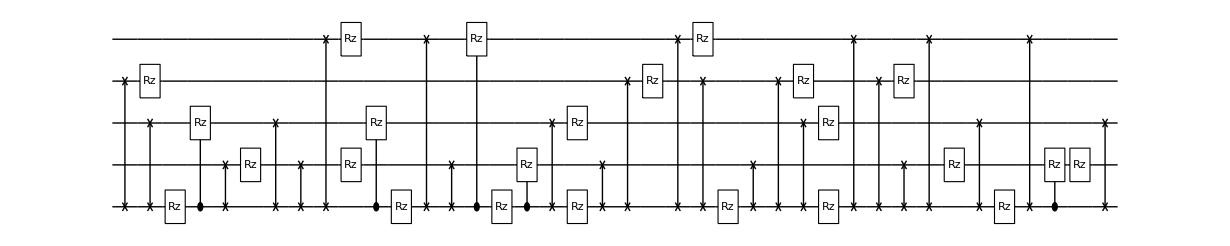

**** Compile @Thu 29 Dec 2022 03:11:55 τ=8.; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 03:26:58 completed with ngates=43, cost=0.000017012470231891896, at eval=2527

τ=8.2; δ=0.2; cost=3.39589×10^-6; ngates=48; runtime=21.562 min

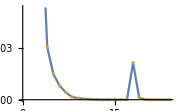

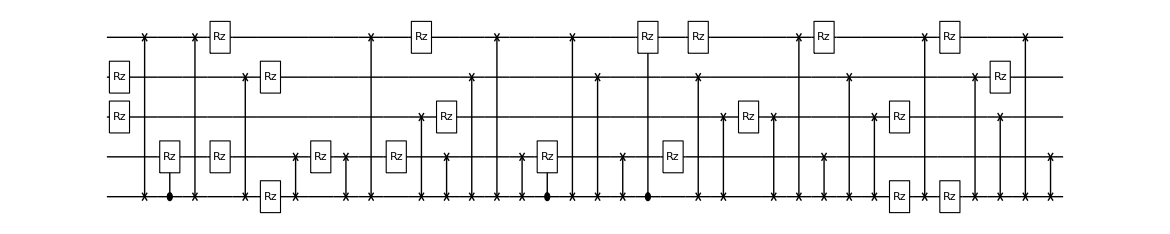

**** Compile @Thu 29 Dec 2022 03:33:35 τ=8.2; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 03:49:53 completed with ngates=47, cost=9.167212382421575e-6, at eval=2669

τ=8.4; δ=0.2; cost=9.16721×10^-6; ngates=47; runtime=17.822 min

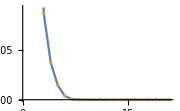

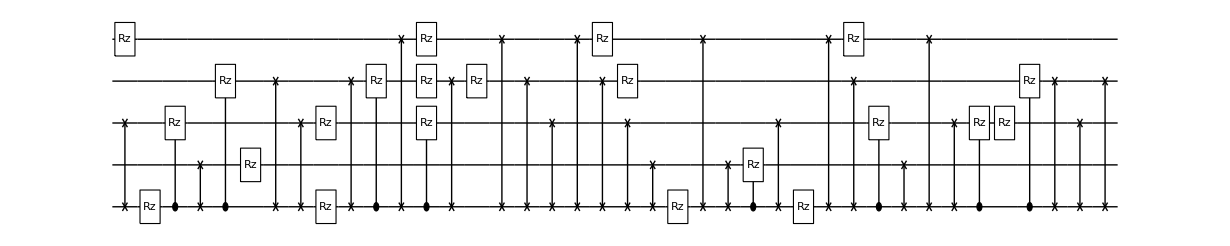

**** Compile @Thu 29 Dec 2022 03:51:31 τ=8.4; δ0.2 ****

τ=8.6; δ=0.2; cost=2.63434×10^-6; ngates=58; runtime=11.7901 min

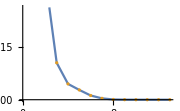

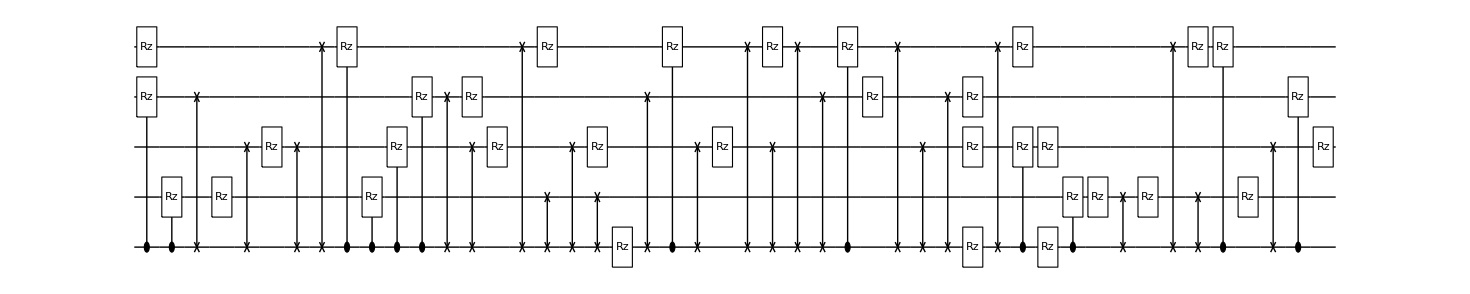

**** Compile @Thu 29 Dec 2022 04:03:25 τ=8.6; δ0.2 ****

τ=8.8; δ=0.2; cost=3.93485×10^-6; ngates=43; runtime=10.0139 min

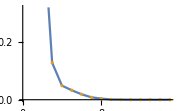

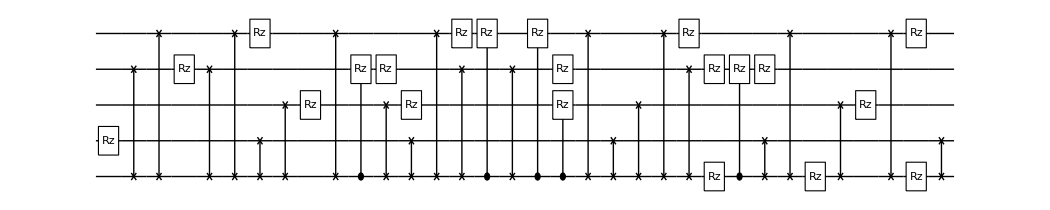

**** Compile @Thu 29 Dec 2022 04:13:32 τ=8.8; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 04:27:50 completed with ngates=40, cost=9.84928164615706e-6, at eval=2485

τ=9.; δ=0.2; cost=4.46482×10^-6; ngates=40; runtime=15.3153 min

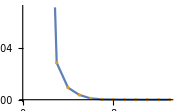

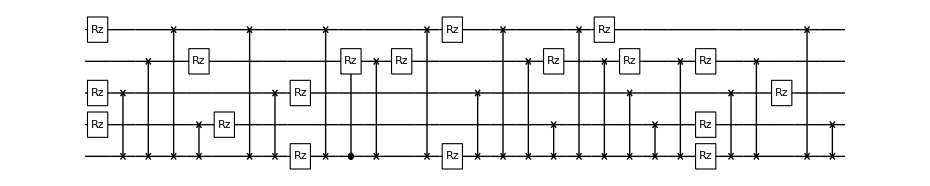

**** Compile @Thu 29 Dec 2022 04:28:55 τ=9.; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 04:43:01 completed with ngates=39, cost=0.000014782037018878924, at eval=2559

Cycle 2@Thu 29 Dec 2022 04:46:11 adjust hyperparams, slowdown:True

τ=9.2; δ=0.2; cost=2.8327×10^-6; ngates=47; runtime=23.7512 min

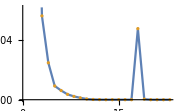

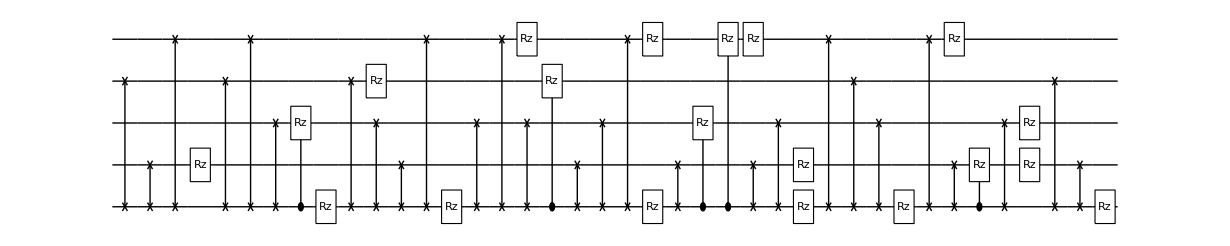

**** Compile @Thu 29 Dec 2022 04:52:45 τ=9.2; δ0.2 ****

τ=9.4; δ=0.2; cost=1.96316×10^-6; ngates=46; runtime=7.25642 min

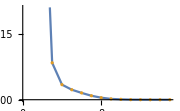

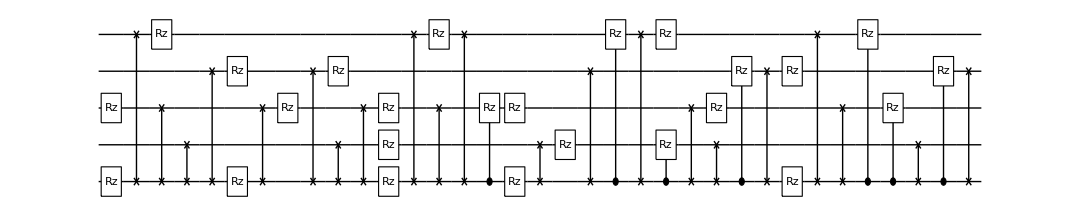

**** Compile @Thu 29 Dec 2022 05:00:03 τ=9.4; δ0.2 ****

τ=9.6; δ=0.2; cost=1.69583×10^-6; ngates=42; runtime=6.62015 min

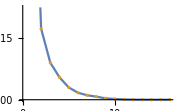

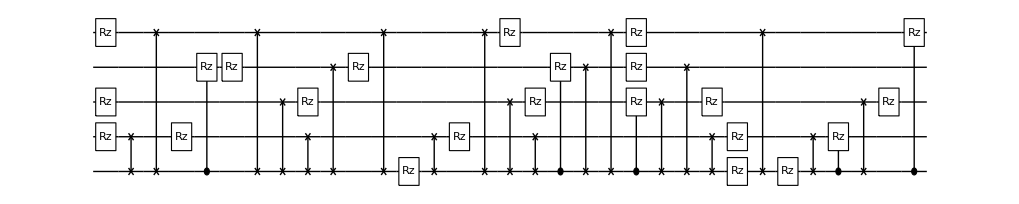

**** Compile @Thu 29 Dec 2022 05:06:43 τ=9.6; δ0.2 ****

τ=9.8; δ=0.2; cost=4.24165×10^-6; ngates=38; runtime=9.91832 min

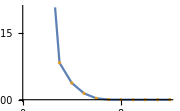

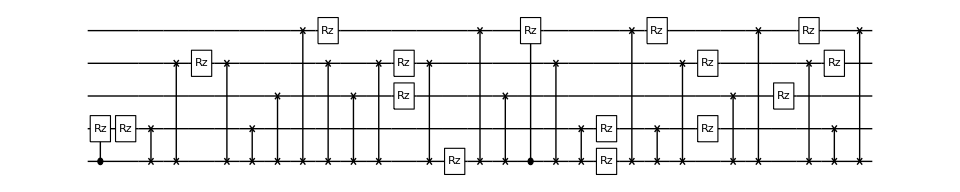

**** Compile @Thu 29 Dec 2022 05:16:44 τ=9.8; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 05:30:36 completed with ngates=37, cost=8.936267117176655e-6, at eval=2174

τ=10.; δ=0.2; cost=8.93627×10^-6; ngates=37; runtime=15.334 min

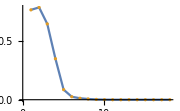

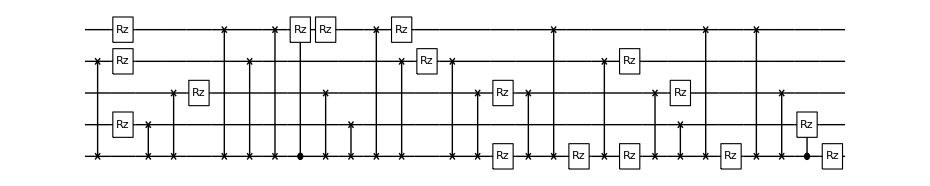

**** Compile @Thu 29 Dec 2022 05:32:11 τ=10.; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 05:45:28 completed with ngates=42, cost=5.366357488933993e-6, at eval=2172

τ=10.2; δ=0.2; cost=5.36636×10^-6; ngates=42; runtime=14.3926 min

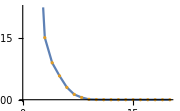

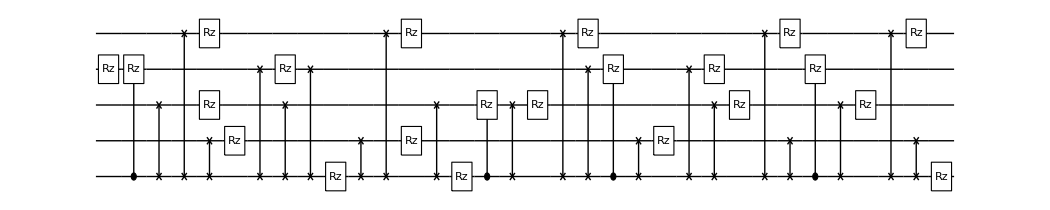

**** Compile @Thu 29 Dec 2022 05:46:40 τ=10.2; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 06:01:35 completed with ngates=39, cost=0.000019338080516573264, at eval=2743

τ=10.4; δ=0.2; cost=7.07529×10^-7; ngates=39; runtime=15.99 min

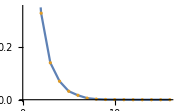

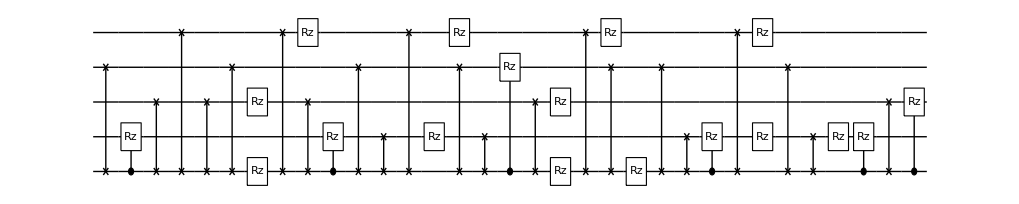

**** Compile @Thu 29 Dec 2022 06:02:46 τ=10.4; δ0.2 ****

τ=10.6; δ=0.2; cost=4.35269×10^-6; ngates=39; runtime=13.6756 min

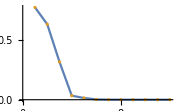

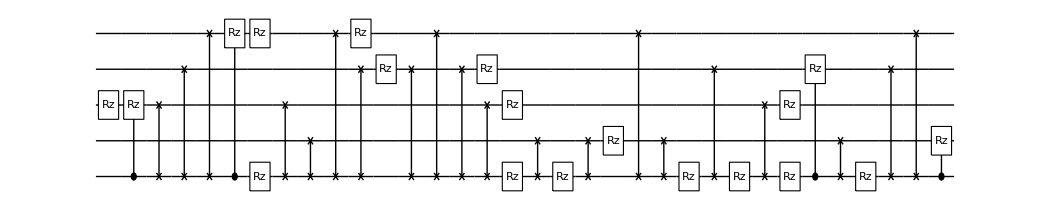

**** Compile @Thu 29 Dec 2022 06:16:33 τ=10.6; δ0.2 ****

τ=10.8; δ=0.2; cost=7.16266×10^-6; ngates=37; runtime=10.2673 min

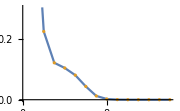

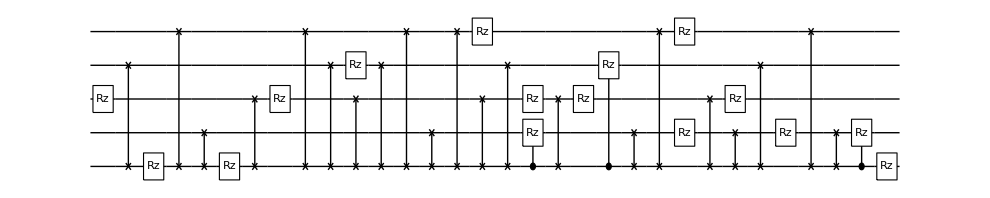

**** Compile @Thu 29 Dec 2022 06:26:52 τ=10.8; δ0.2 ****

τ=11.; δ=0.2; cost=5.81716×10^-6; ngates=48; runtime=5.96752 min

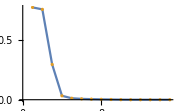

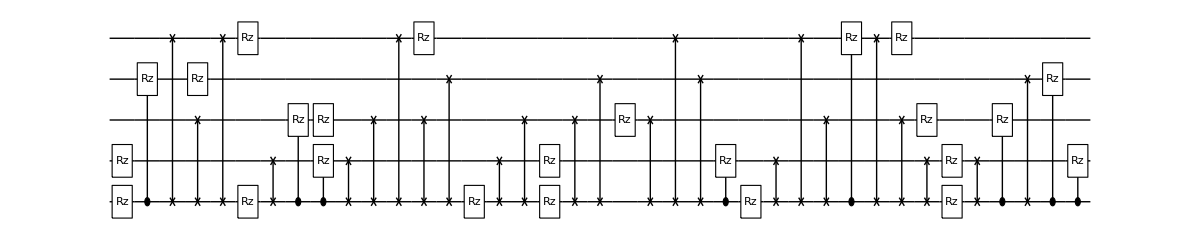

**** Compile @Thu 29 Dec 2022 06:32:51 τ=11.; δ0.2 ****

τ=11.2; δ=0.2; cost=8.96034×10^-6; ngates=48; runtime=5.30464 min

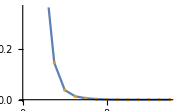

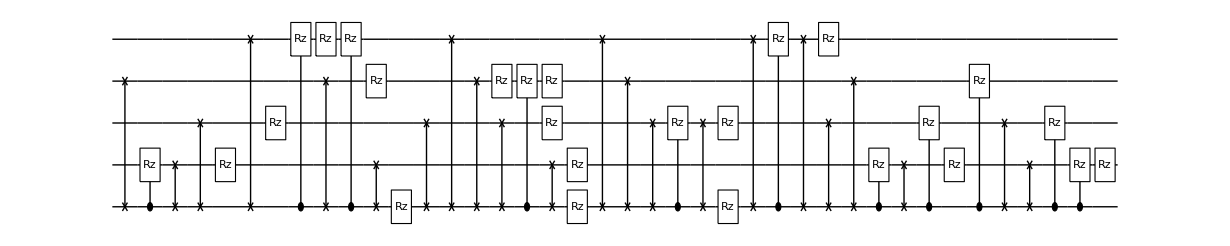

**** Compile @Thu 29 Dec 2022 06:38:16 τ=11.2; δ0.2 ****

τ=11.4; δ=0.2; cost=3.60486×10^-6; ngates=45; runtime=8.03767 min

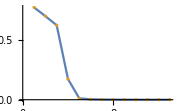

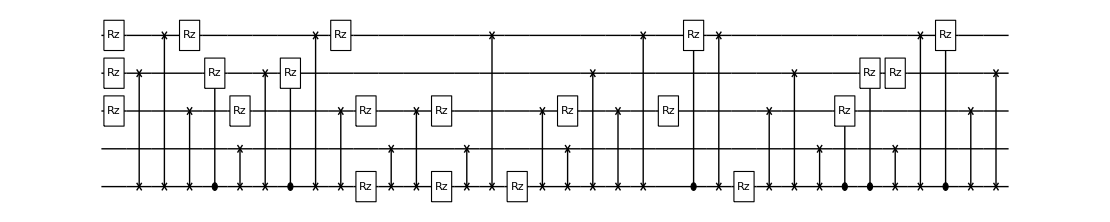

**** Compile @Thu 29 Dec 2022 06:46:24 τ=11.4; δ0.2 ****

τ=11.6; δ=0.2; cost=7.05058×10^-6; ngates=38; runtime=7.73236 min

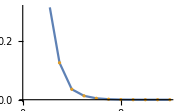

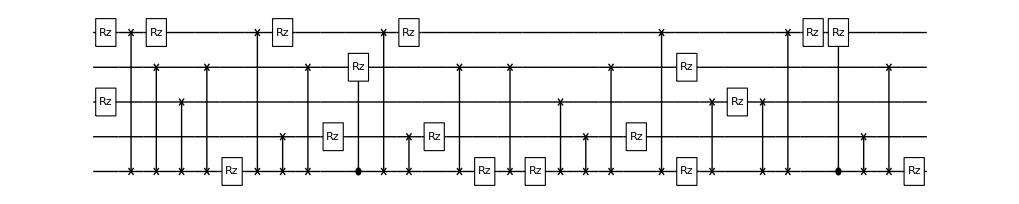

**** Compile @Thu 29 Dec 2022 06:54:08 τ=11.6; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 07:07:40 completed with ngates=40, cost=3.886460529956004e-6, at eval=2171

τ=11.8; δ=0.2; cost=3.67796×10^-6; ngates=40; runtime=14.8919 min

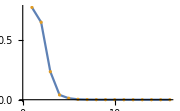

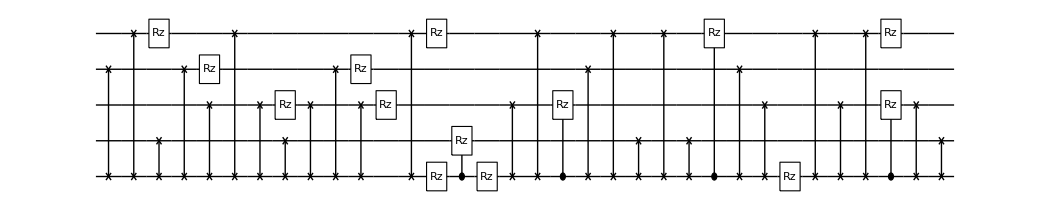

**** Compile @Thu 29 Dec 2022 07:09:03 τ=11.8; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 07:22:23 completed with ngates=40, cost=4.7192818739549836e-6, at eval=2331

τ=12.; δ=0.2; cost=1.21682×10^-6; ngates=40; runtime=14.6871 min

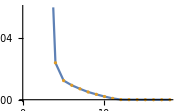

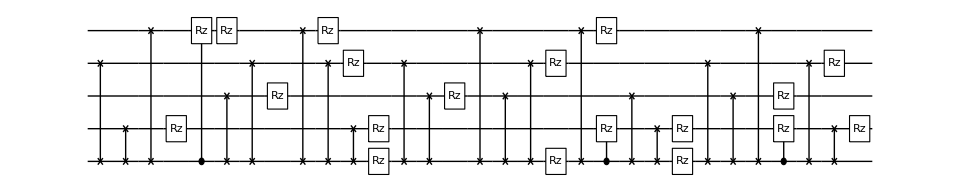

**** Compile @Thu 29 Dec 2022 07:23:48 τ=12.; δ0.2 ****

τ=12.2; δ=0.2; cost=5.62287×10^-6; ngates=46; runtime=6.89677 min

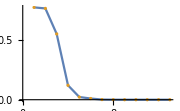

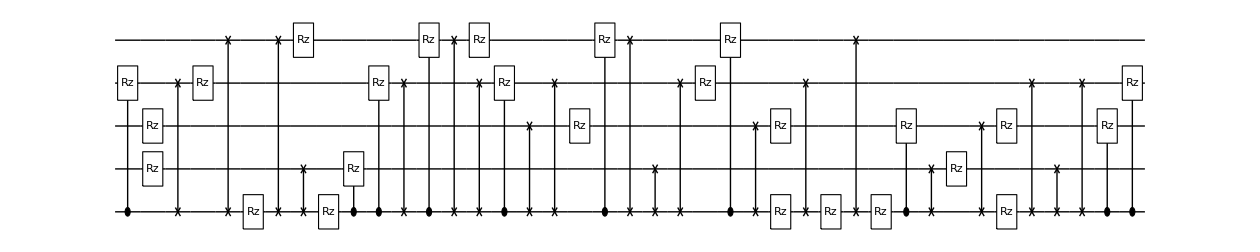

**** Compile @Thu 29 Dec 2022 07:30:45 τ=12.2; δ0.2 ****

τ=12.4; δ=0.2; cost=4.95669×10^-6; ngates=44; runtime=12.3671 min

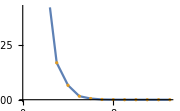

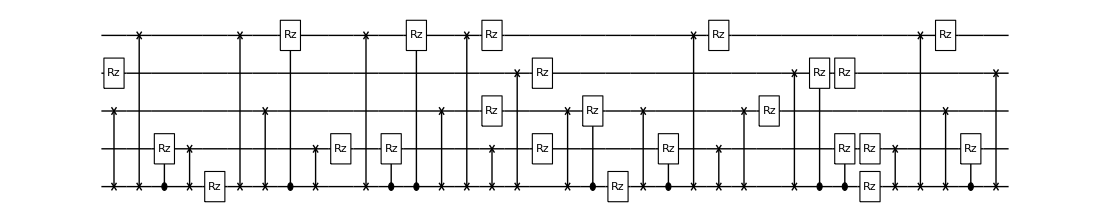

**** Compile @Thu 29 Dec 2022 07:43:13 τ=12.4; δ0.2 ****

τ=12.6; δ=0.2; cost=9.60756×10^-6; ngates=47; runtime=10.3391 min

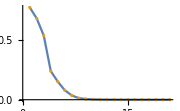

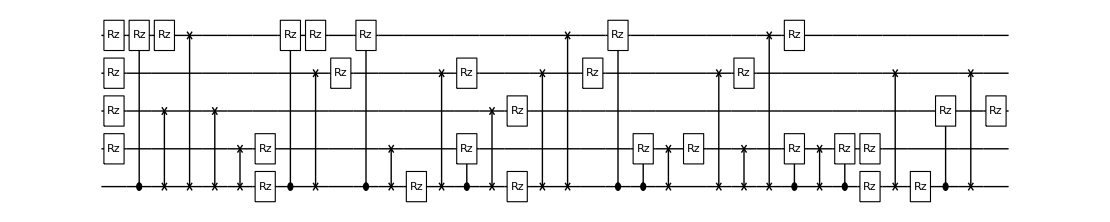

**** Compile @Thu 29 Dec 2022 07:53:39 τ=12.6; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 08:07:38 completed with ngates=40, cost=0.000011088539780157447, at eval=2208

τ=12.8; δ=0.2; cost=7.32653×10^-6; ngates=40; runtime=15.7881 min

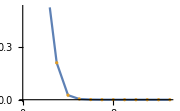

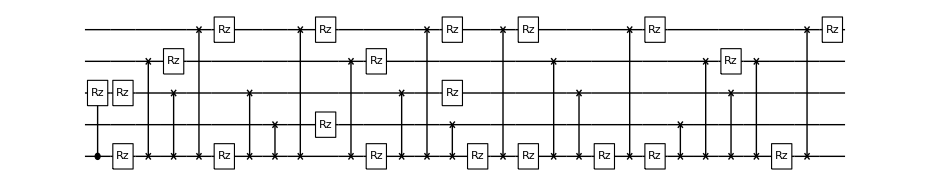

**** Compile @Thu 29 Dec 2022 08:09:30 τ=12.8; δ0.2 ****

τ=13.; δ=0.2; cost=4.6664×10^-6; ngates=43; runtime=11.7005 min

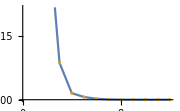

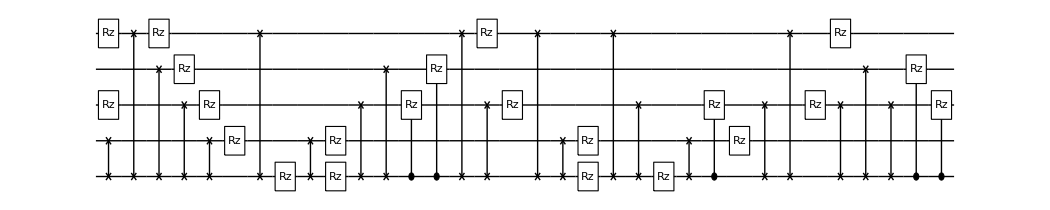

**** Compile @Thu 29 Dec 2022 08:21:18 τ=13.; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 08:36:03 completed with ngates=44, cost=0.000015914379475345797, at eval=2154

τ=13.2; δ=0.2; cost=5.86961×10^-6; ngates=44; runtime=16.5933 min

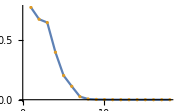

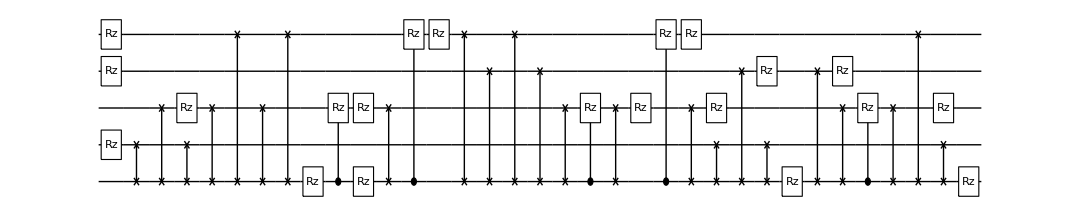

**** Compile @Thu 29 Dec 2022 08:38:00 τ=13.2; δ0.2 ****

τ=13.4; δ=0.2; cost=4.11482×10^-6; ngates=50; runtime=15.3505 min

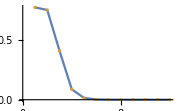

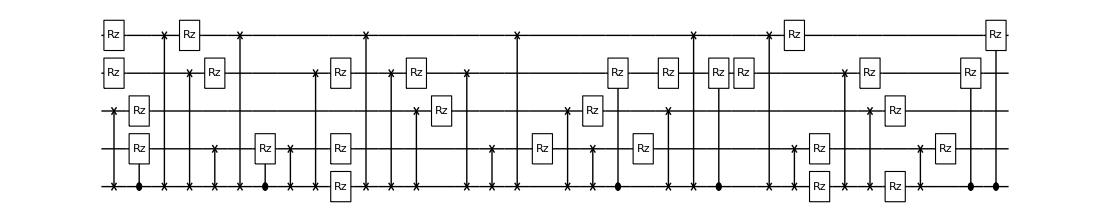

**** Compile @Thu 29 Dec 2022 08:53:27 τ=13.4; δ0.2 ****

τ=13.6; δ=0.2; cost=3.24017×10^-6; ngates=43; runtime=8.72334 min

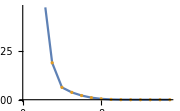

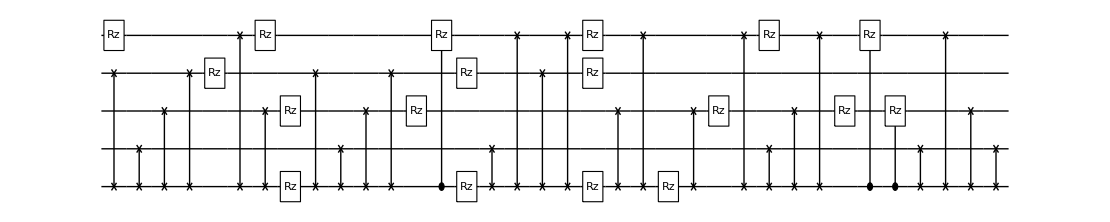

**** Compile @Thu 29 Dec 2022 09:02:16 τ=13.6; δ0.2 ****

τ=13.8; δ=0.2; cost=4.29683×10^-6; ngates=47; runtime=5.26378 min

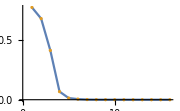

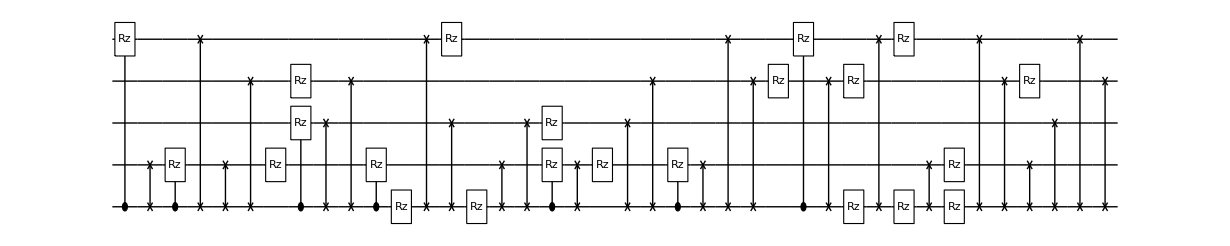

**** Compile @Thu 29 Dec 2022 09:07:32 τ=13.8; δ0.2 ****

τ=14.; δ=0.2; cost=6.716×10^-6; ngates=35; runtime=6.24092 min

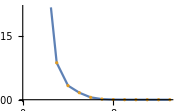

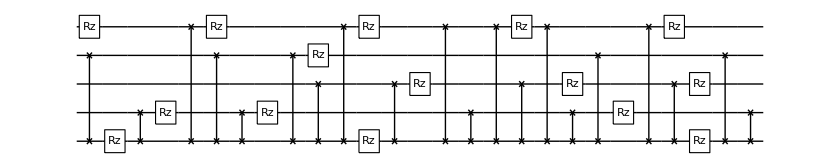

**** Compile @Thu 29 Dec 2022 09:13:47 τ=14.; δ0.2 ****

τ=14.2; δ=0.2; cost=6.50463×10^-6; ngates=42; runtime=10.0868 min

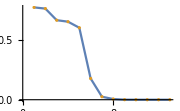

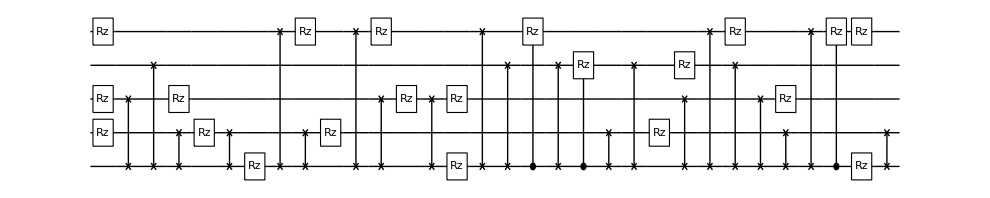

**** Compile @Thu 29 Dec 2022 09:23:52 τ=14.2; δ0.2 ****

τ=14.4; δ=0.2; cost=1.76823×10^-6; ngates=39; runtime=11.8181 min

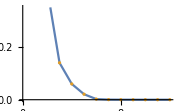

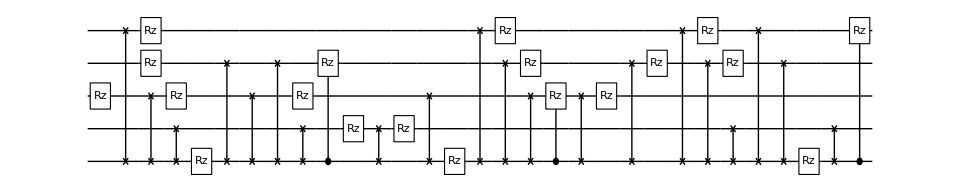

**** Compile @Thu 29 Dec 2022 09:35:42 τ=14.4; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 09:48:31 completed with ngates=36, cost=0.000011686128332799584, at eval=2213

τ=14.6; δ=0.2; cost=3.17335×10^-6; ngates=36; runtime=13.9785 min

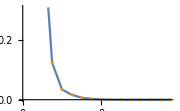

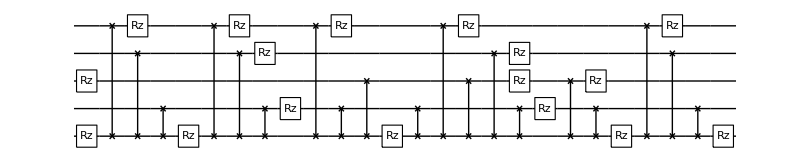

**** Compile @Thu 29 Dec 2022 09:49:42 τ=14.6; δ0.2 ****

τ=14.8; δ=0.2; cost=3.34041×10^-6; ngates=43; runtime=4.66354 min

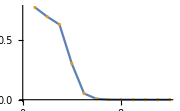

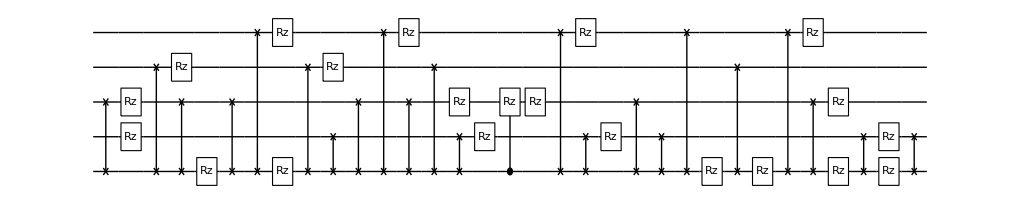

**** Compile @Thu 29 Dec 2022 09:54:24 τ=14.8; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 10:07:01 completed with ngates=40, cost=0.00001280517543844617, at eval=2128

τ=15.; δ=0.2; cost=2.87544×10^-6; ngates=37; runtime=16.6247 min

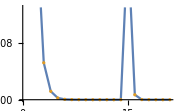

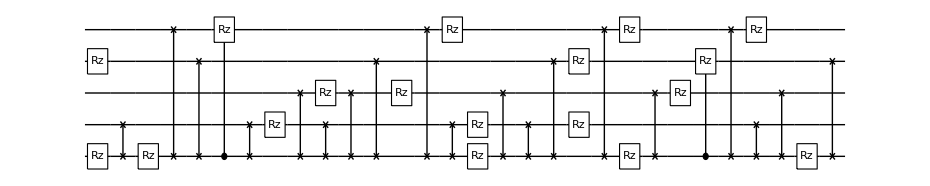

**** Compile @Thu 29 Dec 2022 10:11:01 τ=15.; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 10:24:21 completed with ngates=45, cost=8.894940823567232e-6, at eval=2129

τ=15.2; δ=0.2; cost=7.2×10^-6; ngates=45; runtime=14.5783 min

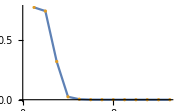

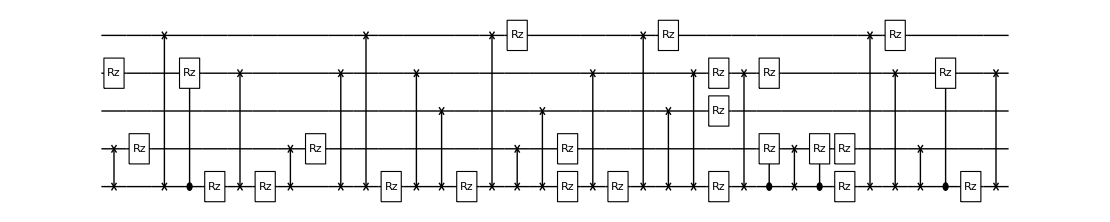

**** Compile @Thu 29 Dec 2022 10:25:38 τ=15.2; δ0.2 ****

τ=15.4; δ=0.2; cost=7.8149×10^-6; ngates=45; runtime=7.68989 min

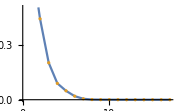

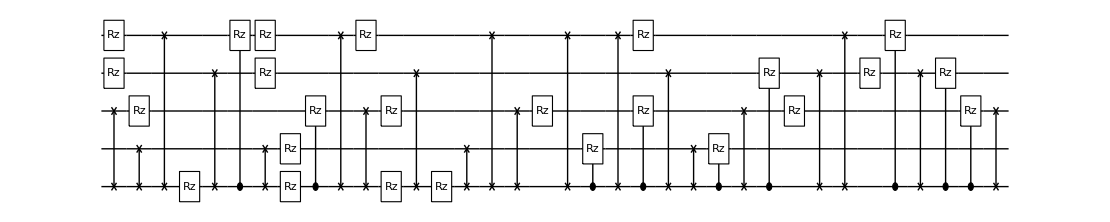

**** Compile @Thu 29 Dec 2022 10:33:21 τ=15.4; δ0.2 ****

τ=15.6; δ=0.2; cost=3.47837×10^-6; ngates=37; runtime=7.724 min

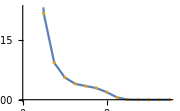

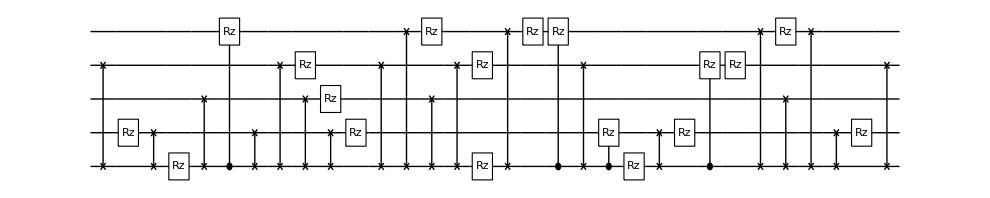

**** Compile @Thu 29 Dec 2022 10:41:06 τ=15.6; δ0.2 ****

τ=15.8; δ=0.2; cost=2.63818×10^-6; ngates=38; runtime=10.4683 min

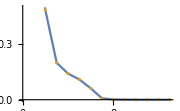

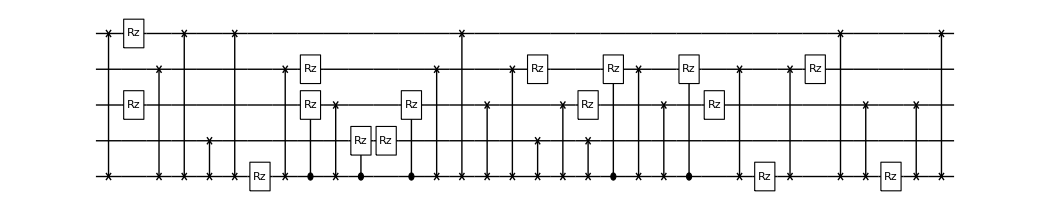

**** Compile @Thu 29 Dec 2022 10:51:34 τ=15.8; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 11:04:59 completed with ngates=39, cost=6.094653626553814e-6, at eval=2234

τ=16.; δ=0.2; cost=6.09465×10^-6; ngates=39; runtime=14.6506 min

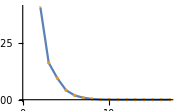

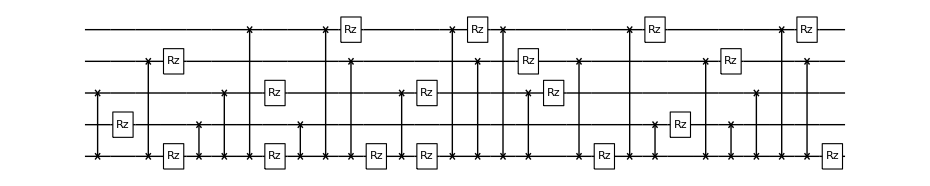

**** Compile @Thu 29 Dec 2022 11:06:14 τ=16.; δ0.2 ****

τ=16.2; δ=0.2; cost=3.08773×10^-6; ngates=44; runtime=5.11954 min

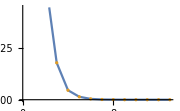

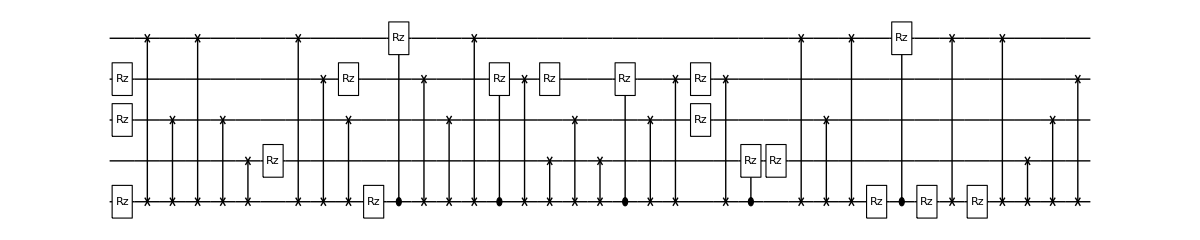

**** Compile @Thu 29 Dec 2022 11:11:25 τ=16.2; δ0.2 ****

τ=16.4; δ=0.2; cost=9.81357×10^-6; ngates=40; runtime=10.0418 min

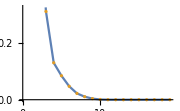

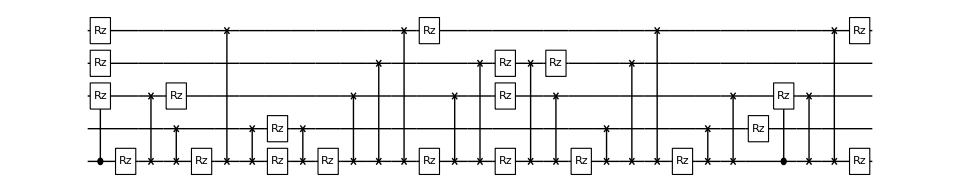

**** Compile @Thu 29 Dec 2022 11:21:27 τ=16.4; δ0.2 ****

τ=16.6; δ=0.2; cost=7.2391×10^-6; ngates=41; runtime=6.75973 min

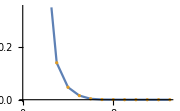

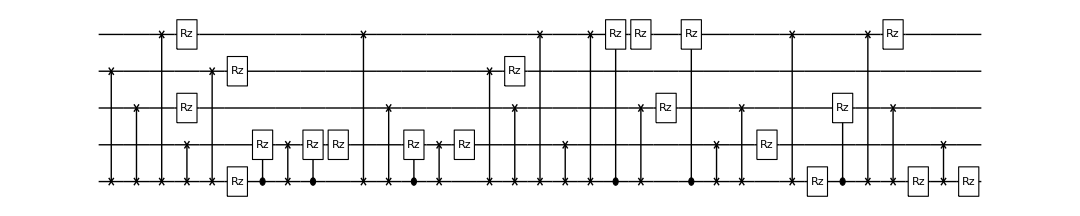

**** Compile @Thu 29 Dec 2022 11:28:13 τ=16.6; δ0.2 ****

τ=16.8; δ=0.2; cost=2.62654×10^-6; ngates=48; runtime=7.82827 min

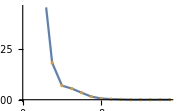

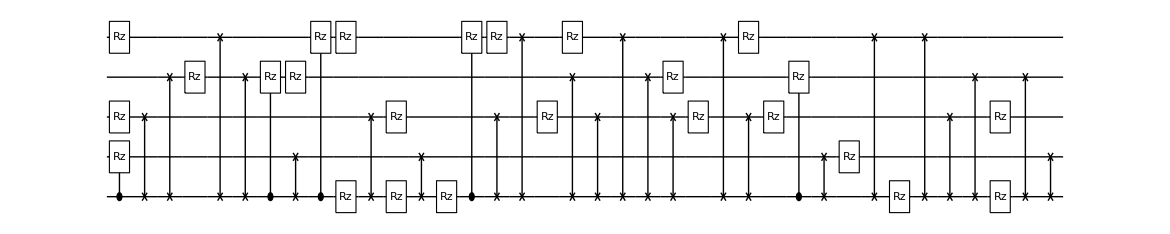

**** Compile @Thu 29 Dec 2022 11:36:04 τ=16.8; δ0.2 ****

τ=17.; δ=0.2; cost=7.77929×10^-6; ngates=51; runtime=14.2775 min

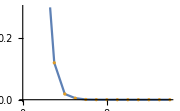

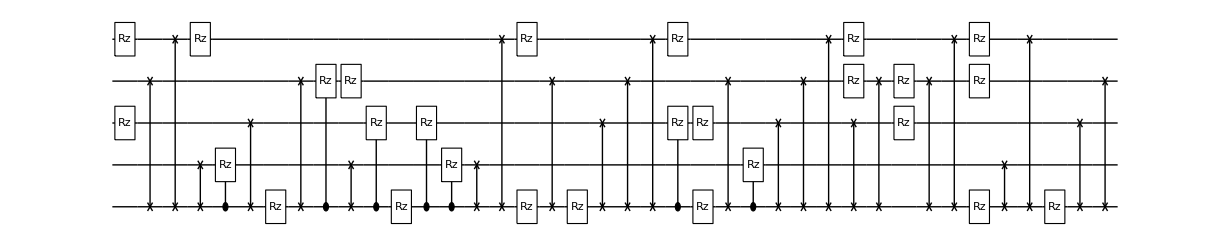

**** Compile @Thu 29 Dec 2022 11:50:23 τ=17.; δ0.2 ****

τ=17.2; δ=0.2; cost=7.2612×10^-6; ngates=40; runtime=13.1755 min

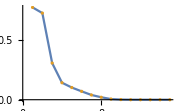

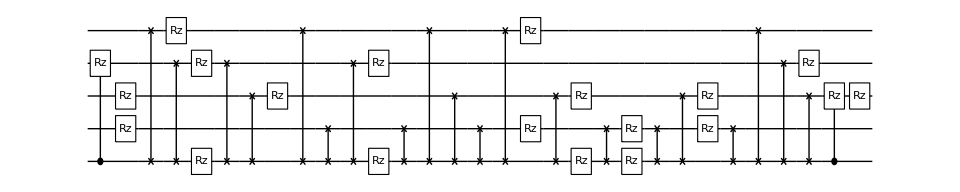

**** Compile @Thu 29 Dec 2022 12:03:36 τ=17.2; δ0.2 ****

τ=17.4; δ=0.2; cost=6.04937×10^-6; ngates=39; runtime=7.17803 min

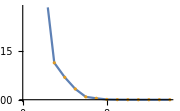

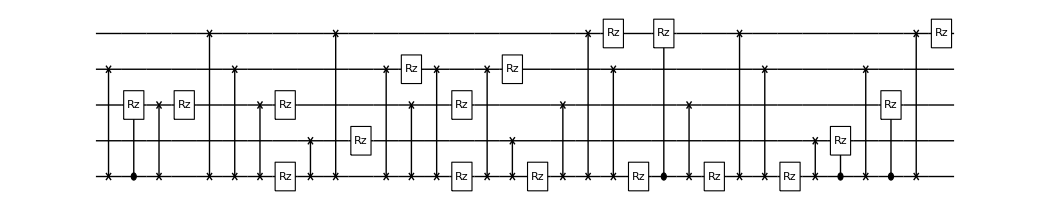

**** Compile @Thu 29 Dec 2022 12:10:50 τ=17.4; δ0.2 ****

τ=17.6; δ=0.2; cost=5.21365×10^-6; ngates=51; runtime=9.89017 min

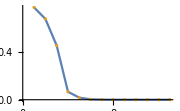

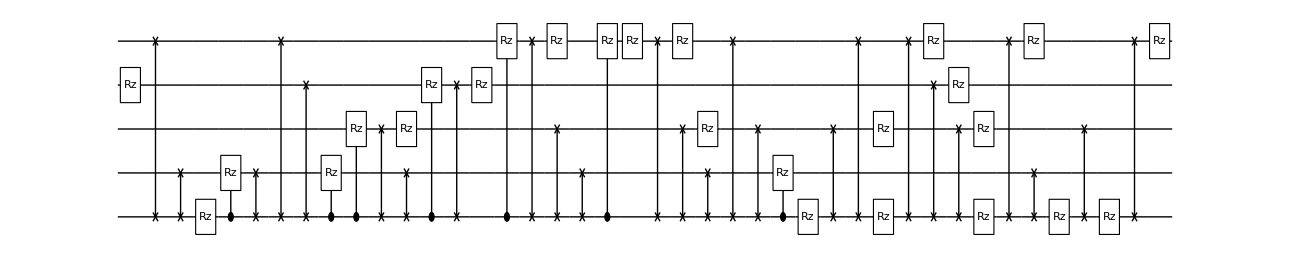

**** Compile @Thu 29 Dec 2022 12:20:50 τ=17.6; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 12:33:48 completed with ngates=39, cost=8.690981014081167e-6, at eval=2185

τ=17.8; δ=0.2; cost=6.43369×10^-6; ngates=39; runtime=14.3976 min

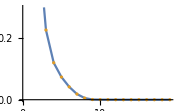

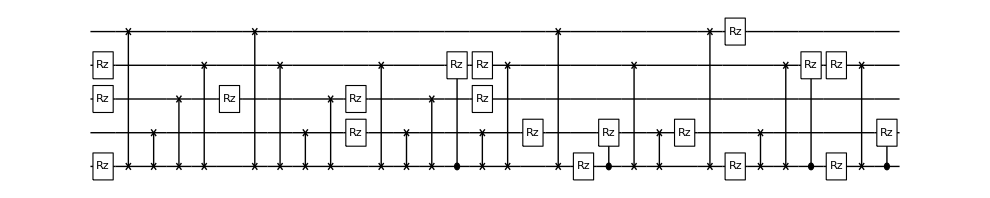

**** Compile @Thu 29 Dec 2022 12:35:15 τ=17.8; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 12:49:18 completed with ngates=43, cost=0.000014396344578004872, at eval=2100

Cycle 2@Thu 29 Dec 2022 12:53:17 adjust hyperparams, slowdown:True

τ=18.; δ=0.2; cost=4.829×10^-6; ngates=43; runtime=26.8728 min

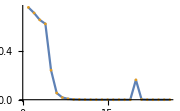

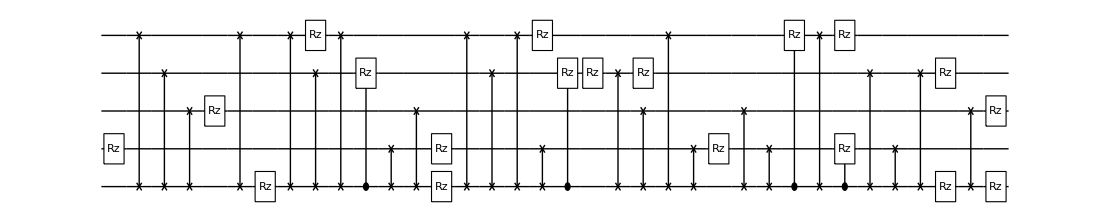

**** Compile @Thu 29 Dec 2022 13:02:09 τ=18.; δ0.2 ****

τ=18.2; δ=0.2; cost=3.87519×10^-6; ngates=47; runtime=10.1878 min

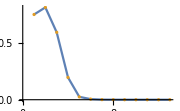

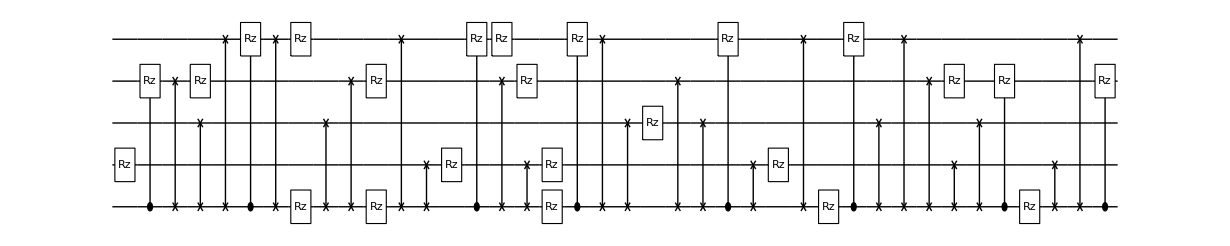

**** Compile @Thu 29 Dec 2022 13:12:23 τ=18.2; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 13:26:18 completed with ngates=47, cost=6.0239531264327795e-6, at eval=2141

τ=18.4; δ=0.2; cost=6.02395×10^-6; ngates=47; runtime=15.2469 min

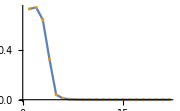

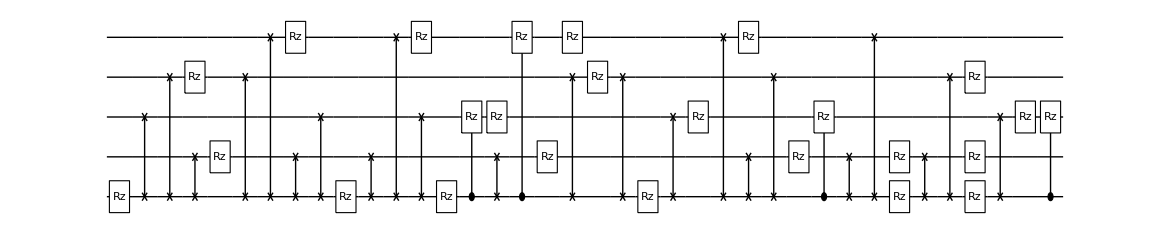

**** Compile @Thu 29 Dec 2022 13:27:44 τ=18.4; δ0.2 ****

τ=18.6; δ=0.2; cost=7.53555×10^-6; ngates=50; runtime=6.97912 min

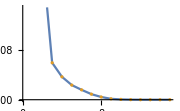

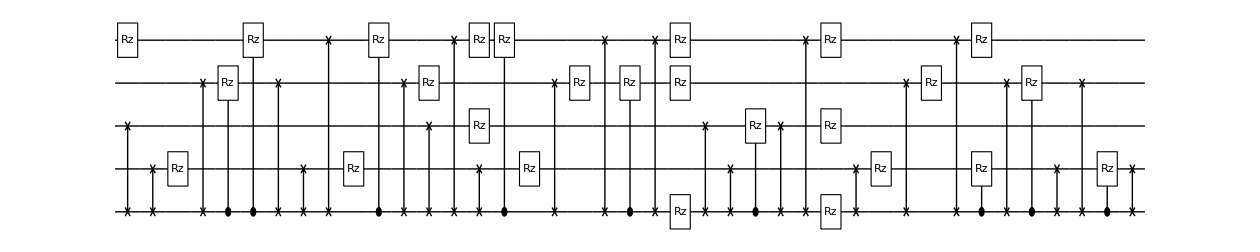

**** Compile @Thu 29 Dec 2022 13:34:48 τ=18.6; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 13:49:28 completed with ngates=45, cost=0.000013425006149425656, at eval=2203

τ=18.8; δ=0.2; cost=8.53004×10^-6; ngates=45; runtime=16.1219 min

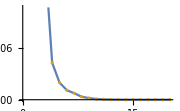

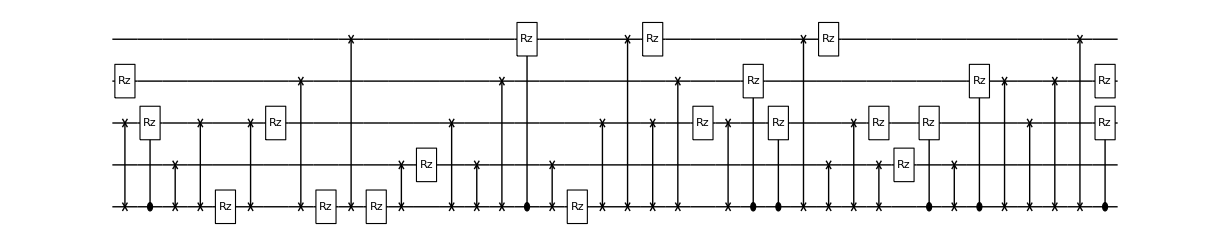

**** Compile @Thu 29 Dec 2022 13:50:58 τ=18.8; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 14:05:25 completed with ngates=41, cost=0.000010602236704571055, at eval=2543

τ=19.; δ=0.2; cost=7.13006×10^-6; ngates=41; runtime=15.4297 min

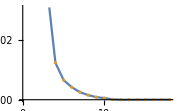

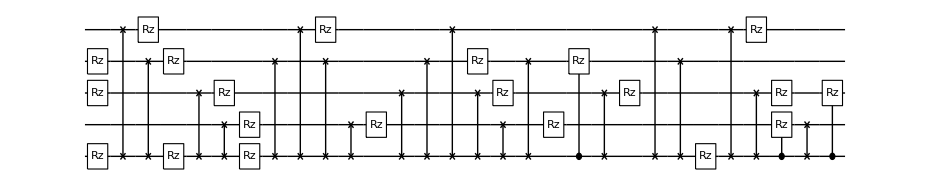

**** Compile @Thu 29 Dec 2022 14:06:27 τ=19.; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 14:19:58 completed with ngates=41, cost=0.000011265059711274006, at eval=2187

τ=19.2; δ=0.2; cost=6.73308×10^-6; ngates=41; runtime=14.6913 min

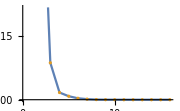

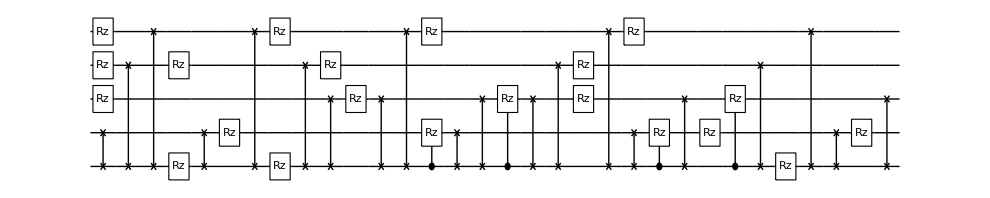

**** Compile @Thu 29 Dec 2022 14:21:10 τ=19.2; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 14:34:33 completed with ngates=42, cost=0.000021541894448029453, at eval=2057

Cycle 2@Thu 29 Dec 2022 14:37:52 adjust hyperparams, slowdown:True

τ=19.4; δ=0.2; cost=4.74507×10^-6; ngates=49; runtime=24.2856 min

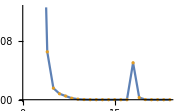

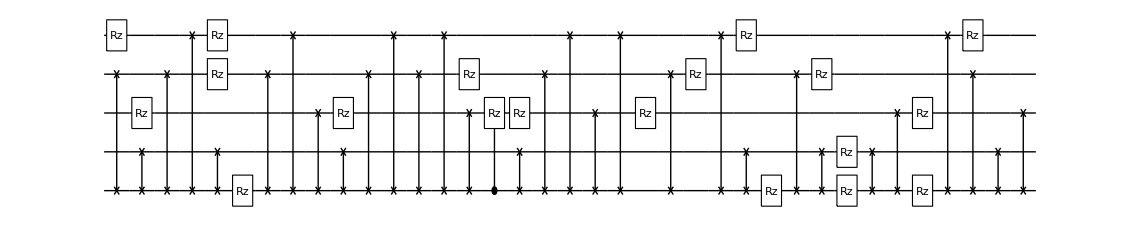

**** Compile @Thu 29 Dec 2022 14:45:34 τ=19.4; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 14:58:58 completed with ngates=46, cost=0.000010473576473324364, at eval=2132

Cycle 2@Thu 29 Dec 2022 15:02:27 adjust hyperparams, slowdown:True

τ=19.6; δ=0.2; cost=2.91162×10^-6; ngates=49; runtime=22.0674 min

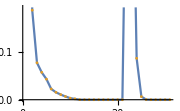

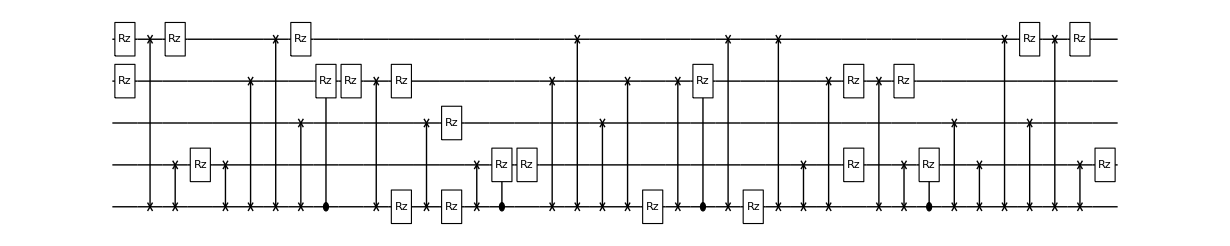

**** Compile @Thu 29 Dec 2022 15:07:44 τ=19.6; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 15:21:59 completed with ngates=44, cost=0.0000241790858055424, at eval=2303

τ=19.8; δ=0.2; cost=7.89288×10^-6; ngates=55; runtime=27.0382 min

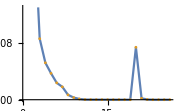

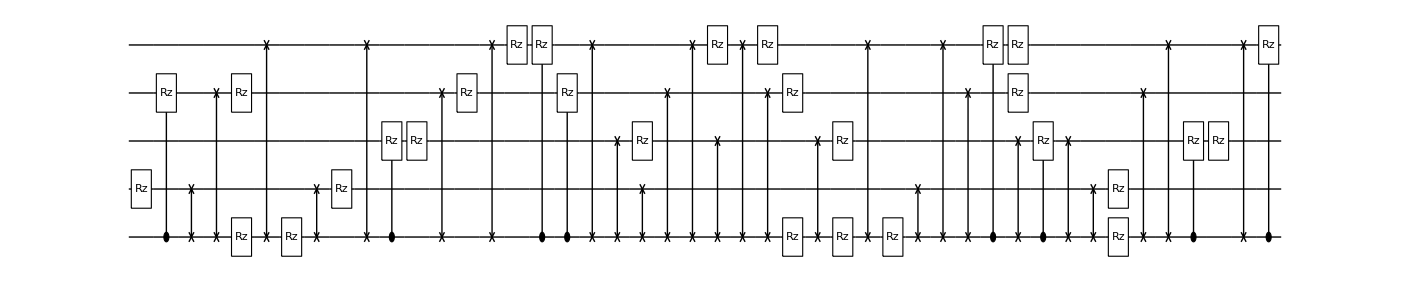

**** Compile @Thu 29 Dec 2022 15:34:52 τ=19.8; δ0.2 ****

Cycle 1@Thu 29 Dec 2022 15:48:17 completed with ngates=40, cost=0.000023940430294855375, at eval=2108

Cycle 2@Thu 29 Dec 2022 15:51:42 adjust hyperparams, slowdown:True

@cycle3, pathetic result.

Cycle 3@Thu 29 Dec 2022 15:59:44 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 0.00001; cost=0.0000176138

τ=20.; δ=0.2; cost=0.0000121203; ngates=40; runtime=25.7757 min

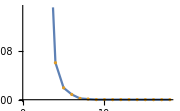

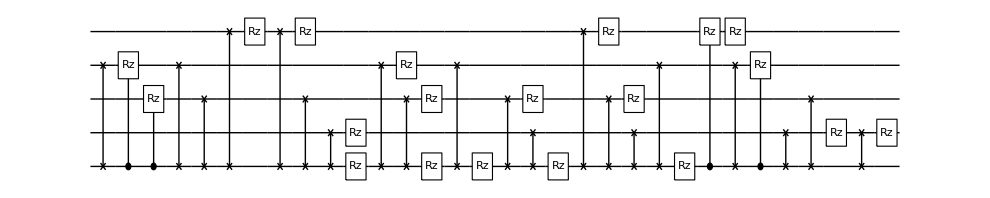

**** Compile @Thu 29 Dec 2022 16:00:44 τ=20.; δ3.5 ****

Cycle 1@Thu 29 Dec 2022 16:15:34 completed with ngates=44, cost=0.000021215929604023742, at eval=2500

Cycle 2@Thu 29 Dec 2022 16:19:12 adjust hyperparams, slowdown:True

@cycle3, pathetic result.

Cycle 3@Thu 29 Dec 2022 16:27:10 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 0.00001; cost=0.0000171861

τ=23.5; δ=3.5; cost=0.0000109027; ngates=44; runtime=27.5932 min

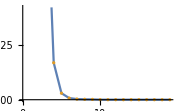

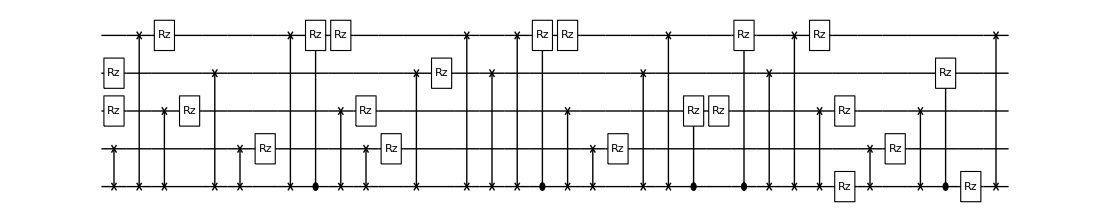

**** Compile @Thu 29 Dec 2022 16:28:21 τ=23.5; δ3.5 ****

Cycle 1@Thu 29 Dec 2022 16:40:52 completed with ngates=40, cost=0.000012627001866771792, at eval=1981

Cycle 2@Thu 29 Dec 2022 16:44:04 adjust hyperparams, slowdown:True

τ=27.; δ=3.5; cost=2.54242×10^-6; ngates=49; runtime=27.9826 min

-Graphics-

-Graphics-

```mathematica
τ=0.
Table[
Print["**** Compile @",DateString[]," τ=",τ, "; δ",δ," ****"];
hbcsmat=Chop@MatrixExp[-ⅈ *δ*CalcPauliStringMatrix[HBCS[5,ϵ,τ]]]; 
DestroyAllQuregs[];
conf=DefaultConfig[5,{1,2,4,8,16}];
res=CJRecompile[5,hbcsmat,conf];
τ+=δ;
AppendTo[bcscompilecssrerun,{τ,δ,res}];
DumpSave["bcscompilecssrerun.mx",bcscompilecssrerun];
{time,Ecur,Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elimmerge,elimbfsmall,elimmetov,elimbf}=res;
Print["τ=",τ, "; δ=",δ,"; cost=",Ecur,"; ngates=",Length@ansatz,"; runtime=",time];
Print@ListPlot[{Elist,Elist},Joined->{True,False},ImageSize->Small];
Print@DrawCircuit[ansatz/.CustomGatesDraw,5];
,{δ,δτ}];
```

The matrixExp vs compiled

```mathematica
(*initialisation*)
{ψexact,ψinitexact}=CreateQuregs[5,2];
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=eigvec[[First@Ordering[eigval,1]]];
SetQuregMatrix[ψinitexact,initv];
```

```mathematica
CloneQureg[ψexact,ψinitexact];
rexactcomp={{0,1}};
Table[
{τ,δ,res}=comp;
ApplyCircuit[ψexact,res[[4]]/.CustomGatesDefinitions/.res[[5]]];
AppendTo[rexactcomp,{τ,CalcFidelity[ψexact,ψinitexact]}]
,{comp, bc}];
```

Table::iterb: Iterator {comp,bcscompilecss2} does not have appropriate bounds.

```mathematica
ListPlot[{rexactot2,rexactcomp},Joined->{True,False},PlotTheme->"Detailed",AspectRatio->0.3,PlotLabel->"Rexact(τ)",ImageSize->Large,FrameTicks->{{Range[1,1.55,0.05],None},{Automatic,None}}]
```

-Graphics-